## Funciones dieléctricas de eritrocitos

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Importación de paquetes

```mathematica
Needs["MaTeX`"]
```

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["KramersKronig`"]
Needs["MieTheory`"]
Needs["GoldenSectionSearchMaxMin`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

GoldenSearchMax::shdw: Symbol GoldenSearchMax appears in multiple contexts {GoldenSectionSearchMaxMin`,Global`}; definitions in context GoldenSectionSearchMaxMin` may shadow or be shadowed by other definitions.

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;

(*tolerancia para el GoldenSectionSeach*)
tolRes=1.*^-8;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> colors,
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};


(*Directorio para guardar las figuras*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\2-Eritrocitos"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\2-Eritrocitos

## Funciones generales

```mathematica
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
eps[parteRe_,parteIm_,x_]:=(parteRe[x]+I parteIm[x])^2;

(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[epsFunc_, intervalos_, tolRes_] := GoldenSearchMax[epsFunc, #1, #2, tolRes] & @@@ intervalos;
  
(*Parte imaginaria de lorentziana*)
lorentzIm[omega_,omega0_,gamma_]:=(gamma omega)/((omega0^2-omega^2)^2+(gamma omega)^2)
(*Suma lorentzianas*)
lorentzSumIm[omega_, A_List, omega0_List, gamma_List] :=  Sum[A[[i]] * lorentzIm[omega, omega0[[i]], gamma[[i]]], {i, Length[A]}]
```

## Datos beta y H2O -> Parte real

```mathematica
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]]
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];

(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
```

InterpolatingFunction[…]

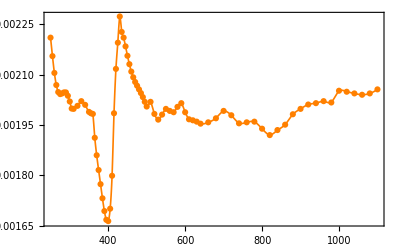

```mathematica
majorTicks=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[200,1100,200]}];

betainterp=Plot[Interpolation[Transpose[{datos1Beta[[All,1]],datos1Beta[[All,2]]}]][λ],{λ,250,1100},PlotStyle -> {Orange,Thickness[0.003]},Evaluate[Sequence @@ plotStyling]];
betaplotpoints=ListPlot[Transpose[{datos1Beta[[All,1]],datos1Beta[[All,2]]}],PlotStyle -> {Orange},Evaluate[Sequence @@ plotStyling]];

betaplot=Show[{betainterp,betaplotpoints}, FrameLabel->{{Style[MaTeX["\\beta(\\lambda)\\:[\\mbox{dL/g}] "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["beta.svg",betaplot]
```

beta.svg

## Concentración 15.3 g/dL

### Importación de datos

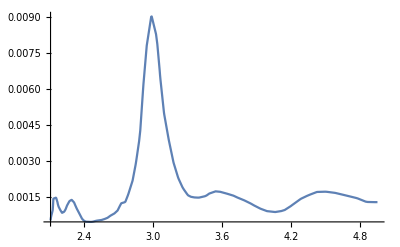

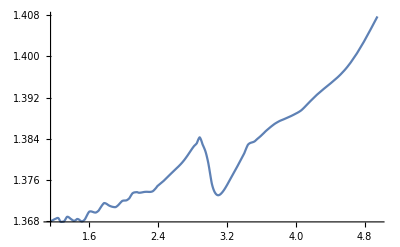

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuA=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\15.3_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA=Drop[datosuA,1];
datos1uA=Map[ToExpression,datos1uA,{2}];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im=h c/datos1uA[[All,1]];
(*Obtener la parte imaginaria del índice de refracción a partir del coeficiente de absorción*)
datos3im=((datos1uA[[All,2]]*10^(-6))/(4*Pi))*datos1uA[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm15=Interpolation[Transpose[{datos2im,datos3im}],InterpolationOrder->1];
parteRe15[x_]:=parteRe[x,15.3]

Plot[parteIm15[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe15[x],{x,1.15,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

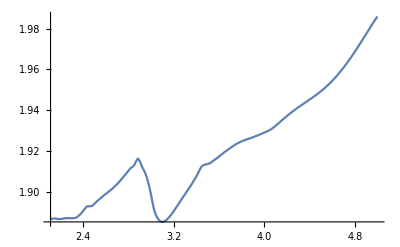

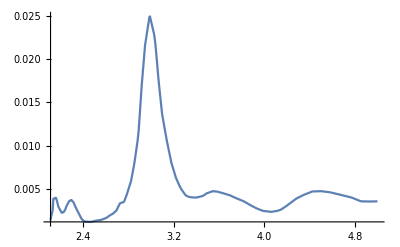

```mathematica
(*Función dieléctrica experimental*)
eps15Im[x_]:=Im[eps[parteRe15,parteIm15,x]];
eps15Re[x_]:=Re[eps[parteRe15,parteIm15,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos15={{2.13,2.15},{2.2,2.3},{2.8,3.2},{3.4,3.7},{4.2,4.7}};

ω0i15=ω0i[eps15Im,intervalos15,tolRes];

Plot[eps15Re[x],{x,2.11,5}]
Plot[eps15Im[x],{x,2.11,5},PlotRange->All]
```

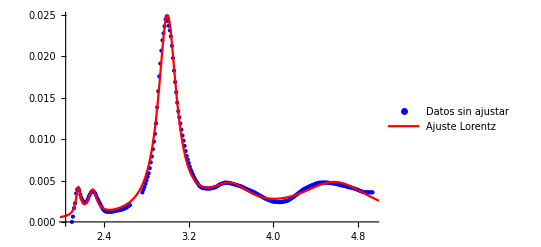

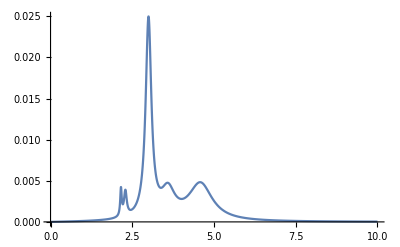

{0.000383064,2.15422,0.0538666,0.000698305,2.28956,0.100709,0.0151476,2.99856,0.20917,0.00602949,3.60037,0.507902,0.0182613,4.60703,0.877683}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin15,xmax15}={Min[datos2im],Max[datos2im]};

eps15Data0=Table[{x,eps15Im[x]},{x,xmin15,2.65,0.01}];
eps15Data1=Table[{x,eps15Im[x]},{x,2.76,xmax15,0.01}];

eps15Data2=Join[eps15Data0,eps15Data1];
eps15Data=Table[{x,eps15Im[x]},{x,xmin15,xmax15,0.01}];

fit15 = NonlinearModelFit[eps15Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i15[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i15[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i15[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i15[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i15[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps15Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit15[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit15[ω],{ω,0,10},PlotRange->All]

fit15Values=Values[fit15["BestFitParameters"]]
```

#### Ajuste pico pequeño

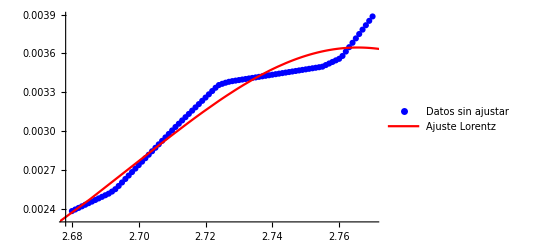

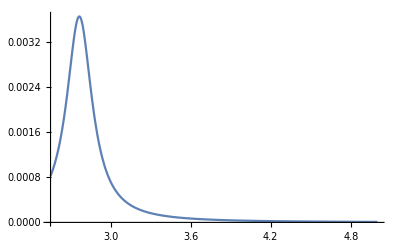

{A1→2.35×10^-3,ω01→2.77,γ1→2.33×10^-1}

{0.00235035,2.76803,0.233036}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps15Data3=Table[{x,eps15Im[x]},{x,2.68,2.77,0.001}];

fit151=NonlinearModelFit[eps15Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];

Show[ListPlot[eps15Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit151[ω],{ω,2.55,3.5},
      PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
      
Plot[fit151[ω],{ω,2.55,5},PlotRange->All]

ScientificForm[fit151["BestFitParameters"],3]
fit151Values=Values[fit151["BestFitParameters"]]
```

#### Ajuste total

```mathematica
fit15tot=NonlinearModelFit[eps15Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},
                         {A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},
                         {A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},
                         {A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},
                         {A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},
                         {A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},
                         ω, Weights->(If[2.6<#<2.8,100,2]&/@(eps15Data[[All,1]]))];

Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit15tot[ω],{ω,xmin15,xmax15},PlotStyle->{Thick,Red},  
        PlotLegends->{"Ajuste Lorentz"},PlotRange->All]];

Plot[fit15tot[ω],{ω,0,10},PlotRange->All];

ScientificForm[fit15tot["BestFitParameters"],3]
```

{A1→4.13×10^-4,ω01→2.15,γ1→5.61×10^-2,A2→6.65×10^-4,ω02→2.29,γ2→9.02×10^-2,A3→1.39×10^-2,ω03→3.,γ3→1.86×10^-1,A4→6.58×10^-3,ω04→3.59,γ4→5.15×10^-1,A5→1.74×10^-2,ω05→4.6,γ5→8.24×10^-1,A6→1.22×10^-5,ω06→2.72,γ6→6.97×10^-3}

{{250.,4.96},{300.,4.13},{350.,3.54},{400.,3.10},{450.,2.76},{500.,2.48},{550.,2.25},{600.,2.07}}

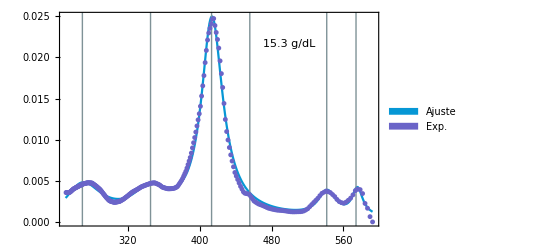

```mathematica
majorTicks15=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}]

interp15=Plot[fit15[h c/λ],{λ,h c/xmax15,h c/xmin15},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/2.16,0},{h c/2.16,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.29,0},{h c/2.29,1}}]},
                        {gris,InfiniteLine[{{h c/3,0},{h c/3,1}}]},
                        {gris,InfiniteLine[{{h c/3.59,0},{h c/3.59,1}}]},
                        {gris,InfiniteLine[{{h c/4.6,0},{h c/4.6,1}}]},
                        {gris,InfiniteLine[{{h c/2.72,0},{h c/2.72,1}}],
                        Inset[Style["15.3 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*)},
              Evaluate[Sequence @@ plotStyling]];
plotpoints15=ListPlot[{h c/#[[1]],#[[2]]}&/@eps15Data,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajuste15=Show[{interp15,plotpoints15}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks15}}]
```

```mathematica
resonancias={2.15,2.29,2.72,3,3.59,4.6};
majorTicksprueba2=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,resonancias}]
Show[{interp15,plotpoints15}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicksprueba2}}]
```

{{576.671,2.15},{541.416,2.29},{455.824,2.72},{413.281,3},{345.36,3.59},{269.531,4.60}}

-Graphics-

### Parte real vía SSKK

```mathematica
omegaprueba15=Range[2.11,4.94,0.01];
parteIm015=Table[fit15tot[x],{x,omegaprueba15}];
parteIm01510=Table[fit15tot[x],{x,omega10}];

datosRealObjetivo15=eps15Re/@omegaprueba15;
```

```mathematica
parteReSSKK15=sskkrebook[omega10,parteIm01510,2.88,eps15Re[2.88]];
partere152=Interpolation[Transpose[{omega10,parteReSSKK15}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 8.76906×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

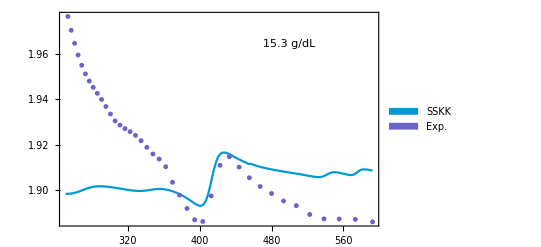

```mathematica
eps15DataRe=Table[{x,eps15Re[x]},{x,xmin15,xmax15,0.07}];

majorTicks15=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}];

interp15sskk=Plot[partere152[h c/λ],{λ,h c/xmax15,h c/xmin15},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["15.3 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  Evaluate[Sequence @@ plotStyling]];

plotpoints15sskk=ListPlot[eps152Re={h c/#[[1]],#[[2]]}&/@eps15DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                          Evaluate[Sequence @@ plotStyling]];

Show[{interp15sskk,plotpoints15sskk}, FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda)"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
                                
                                eps28DataRe=Table[{x,eps28Re[x]},{x,xmin15,xmax15,0.07}];
```

## Concentración 28.7 g/dL

### Importación de datos

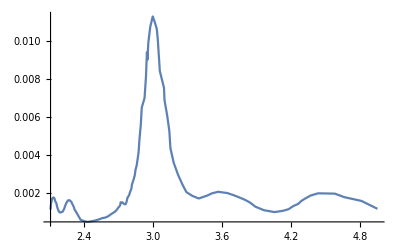

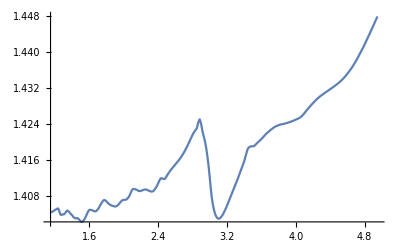

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1];

parteRe28[x_]:=parteRe[x,28.7];

Plot[parteIm28[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe28[x],{x,1.15,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

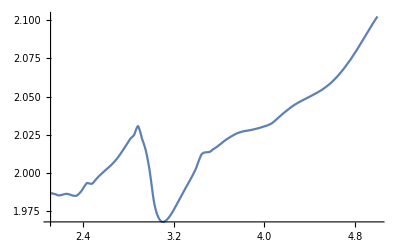

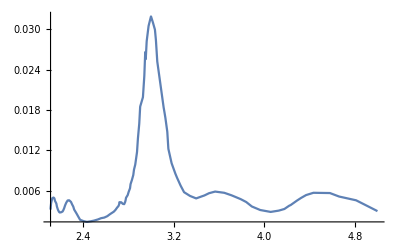

```mathematica
(*Función dieléctrica experimental*)
eps28Im[x_]:=Im[eps[parteRe28,parteIm28,x]];
eps28Re[x_]:=Re[eps[parteRe28,parteIm28,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};

ω0i28=ω0i[eps28Im,intervalos28,tolRes];

Plot[eps28Re[x],{x,2.11,5}]
Plot[eps28Im[x],{x,2.11,5},PlotRange->All]
```

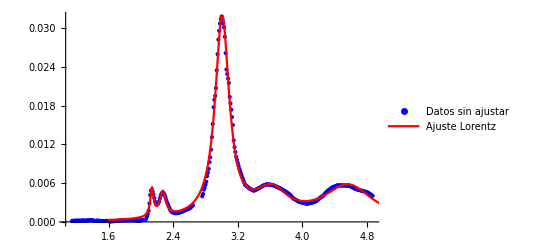

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};

eps28Data0=Table[{x,eps28Im[x]},{x,xmin,2.65,0.01}];
eps28Data1=Table[{x,eps28Im[x]},{x,2.76,xmax,0.01}];
eps28Data2=Join[eps28Data0,eps28Data1];

eps28Data=Table[{x,eps28Im[x]},{x,xmin,xmax,0.01}];
eps28DataLambda=Table[{x,eps28Im[h c/x]},{x,datos1Im[[All,1]]}];

fit28 = NonlinearModelFit[eps28Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i15[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i15[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i15[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i15[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i15[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit28[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit28[ω],{ω,0,10},PlotRange->All];

fit28Values=Values[fit15["BestFitParameters"]];
```

#### Ajuste pico pequeño

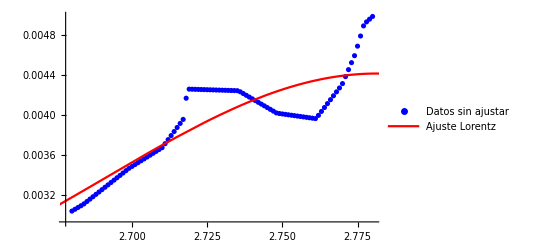

{A1→4.×10^-3,ω01→2.79,γ1→3.25×10^-1}

{0.003998,2.78624,0.325032}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps28Data3=Table[{x,eps28Im[x]},{x,2.68,2.78,0.001}];

fit281=NonlinearModelFit[eps28Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0005},{ω01,2.7},{γ1,0.15}},ω];

Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit281[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
        
ScientificForm[fit281["BestFitParameters"],3]
fit281Values=Values[fit281["BestFitParameters"]]
```

#### Ajuste total

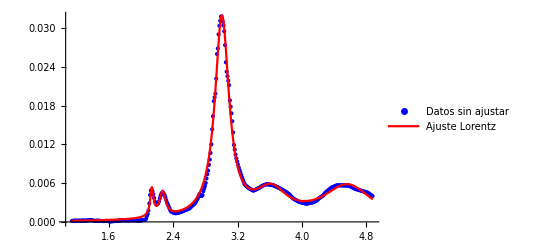

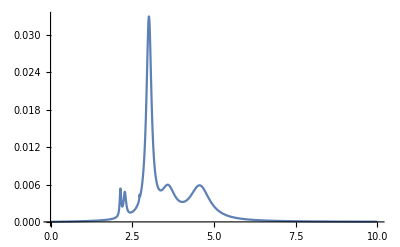

{A1→4.85×10^-4,ω01→2.14,γ1→5.21×10^-2,A2→-8.27×10^-4,ω02→2.27,γ2→-9.33×10^-2,A3→1.8×10^-2,ω03→3.01,γ3→1.87×10^-1,A4→8.45×10^-3,ω04→3.61,γ4→5.23×10^-1,A5→1.84×10^-2,ω05→4.58,γ5→7.38×10^-1,A6→2.55×10^-5,ω06→2.72,γ6→1.31×10^-2}

```mathematica
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},
                         {A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},
                         {A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},
                         {A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},
                         {A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},
                         {A6,fit281Values[[1]]},{ω06,fit281Values[[2]]},{γ6,fit281Values[[3]]}},
                         ω, Weights->(If[2.6<#<2.8,100,2]&/@(eps28Data[[All,1]]))];

Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
          Plot[fit28[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

Plot[fit28tot[ω],{ω,0,10},PlotRange->All]

ScientificForm[fit28tot["BestFitParameters"],3]
```

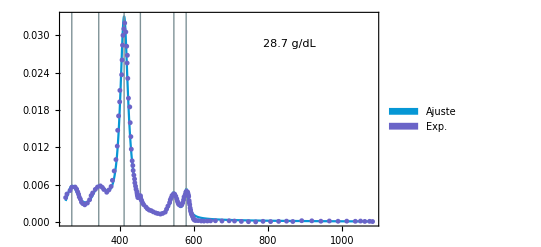

```mathematica
majorTicks28=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,{2.14,2.27,3.01,3.61,4.58,2.72}}];

interp28=Plot[fit28tot[h c/λ],{λ,h c/xmax,h c/xmin},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/2.14,0},{h c/2.14,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.27,0},{h c/2.27,1}}]},
                        {gris,InfiniteLine[{{h c/3.01,0},{h c/3.01,1}}]},
                        {gris,InfiniteLine[{{h c/3.61,0},{h c/3.61,1}}]},
                        {gris,InfiniteLine[{{h c/4.58,0},{h c/4.58,1}}]},
                        {gris,InfiniteLine[{{h c/2.72,0},{h c/2.72,1}}],
                        Inset[Style["28.7 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*)},
              Evaluate[Sequence @@ plotStyling]];
plotpoints28=ListPlot[{#[[1]],#[[2]]}&/@eps28DataLambda,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajuste28=Show[{interp28,plotpoints28}, 
                                 PlotRange->{{Automatic,750},{Automatic,0.032}},
                                FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks28}}]
```

```mathematica
Export["ajusteLorentz28.svg",ajuste28]
```

ajusteLorentz28.svg

### Parte real vía SSKK

```mathematica
parteIm028=Table[fit28[x],{x,1.19,4.96,0.01}];
parteIm02810=Table[fit28[x],{x,omega10}];
omegaprueba28=Range[1.19,4.96,0.01];

datosRealObjetivo28=eps28Re/@omegaprueba28;
                  funcionError28[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
                  epsAnchor=eps28Re[w];
                    (*ejecutar modelo*)espectro=sskkrebook[omegaprueba28,parteIm028,w,epsAnchor];
                      (*error cuadrático total*)dif=espectro-datosRealObjetivo28;
                    Sqrt[Total[dif^2]/Length[datosRealObjetivo28]]];
                    
error28=Table[{w,funcionError28[w]},{w,2.05,3.1,0.01}];
MinimalBy[error28,Last]
```

InterpolatingFunction::dmval: Input value {4.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.89} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.9} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«368»}.

Set::setraw: Cannot assign to raw object 0.00017126.

Set::setraw: Cannot assign to raw object 0.000173603.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

{{2.85,0.037056}}

```mathematica
parteIm02810=Table[fit28tot[x],{x,omega10}];
```

```mathematica
parteReSSKK28=sskkrebook[omega10,parteIm02810,2.85,eps28Re[2.85]];
partere282=Interpolation[Transpose[{omega10,parteReSSKK28}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.02205×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.12713} lies outside the range of data in the interpolating function. Extrapolation will be used.

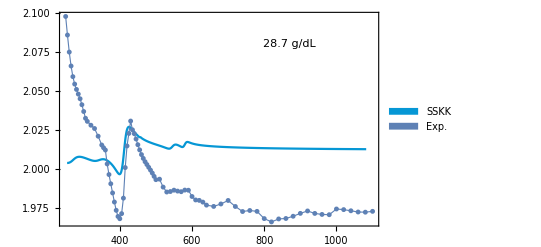

```mathematica
eps28DataRe=Table[{x,eps28Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp28sskk=Plot[partere282[h c/λ],{λ,h c/xmax,h c/xmin},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["28.7 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  Evaluate[Sequence @@ plotStyling]];

plotpoints28sskk=ListPlot[{#[[1]],#[[2]]}&/@eps28DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskk28=Show[{interp28sskk,plotpoints28sskk}, FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskk28.svg",sskk28]
```

sskk28.svg

```mathematica
epsEritrocitosData28=Table[{w*0.2418,partere282[w],fit28tot[w]},{w,1,10,0.01}];
Export["epsEritrocitosData28.csv",epsEritrocitosData28]
```

epsEritrocitosData28.csv

#### Cálculo de la desviación de SSKK de los datos experimentales

```mathematica
Mean[Table[partere282[w]-eps28Re[w],{w,2,3.1,0.01}]]
```

0.0196801

## Concentración 30.6 g/dL

### Importación de datos

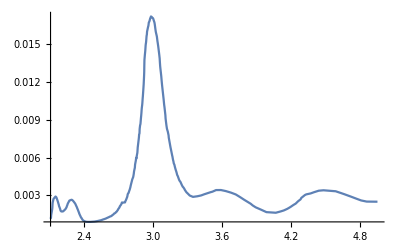

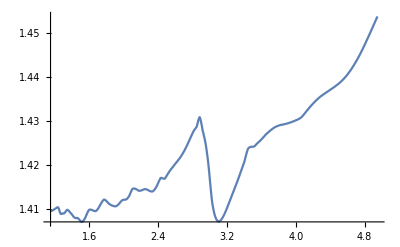

```mathematica
datosuA30=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteIm300=Transpose[{datos1uA30[[All,1]],datos3im30}];
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],InterpolationOrder->1];
parteRe30[x_]:=parteRe[x,30.6]

Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe30[x],{x,1.15,4.95},PlotRange->All]
```

### Cálculo FWHM

```mathematica
(* 1. Definimos el modelo matemático de la Gaussiana con un offset 'b' *)
modelo = a * Exp[-(x - x0)^2 / (2 * sigma^2)] + b;

(* 2. Ejecutamos el ajuste *)
(* NOTA: Es muy recomendable que cambies los valores aproximados iniciales (1, 0, 1, 0) *)
(* por estimaciones reales de tus datos, por ejemplo: {a, Max[datos]} o {x0, posición_del_pico} *)
ajuste = NonlinearModelFit[parteIm300, modelo, {{a, 1}, {x0, 415}, {sigma, 1}, {b, 0}}, x];

(* 3. Extraemos los parámetros optimizados usando reglas de sustitución *)
{bestA, bestX0, bestSigma, bestB} = {a, x0, sigma, b} /. ajuste["BestFitParameters"]

(* 4. Calculamos el FWHM analítico a partir de la sigma óptima *)
fwhm = 2 * Sqrt[2 * Log[2]] * bestSigma;

Print["El FWHM de los datos ajustados es: ", fwhm]
```

{0.0148225,413.517,13.2145,0.00189561}

El FWHM de los datos ajustados es: 31.1179

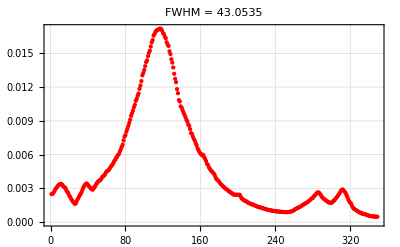

```mathematica
Show[
  ListPlot[datos3im30, PlotStyle -> {Red, PointSize[Medium]}, PlotLabel -> Row[{"FWHM = ", fwhm}]],
  Plot[ajuste[x], {x, Min[datos3im30], Max[datos3im30]}, PlotStyle -> {Blue, Thick}],
  Frame -> True,
  GridLines -> Automatic]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

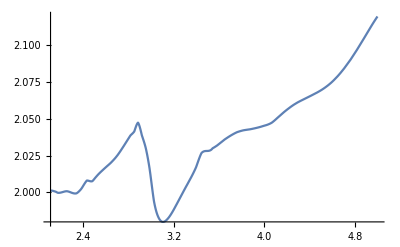

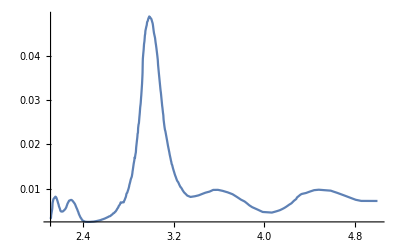

```mathematica
(*Función dieléctrica experimental*)
eps30Im[x_]:=Im[eps[parteRe30,parteIm30,x]];
eps30Re[x_]:=Re[eps[parteRe30,parteIm30,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos30={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};

ω0i30=ω0i[eps30Im,intervalos30,tolRes];

Plot[eps30Re[x],{x,2.11,5}]
Plot[eps30Im[x],{x,2.11,5},PlotRange->All]
```

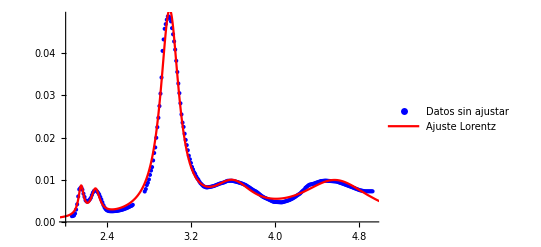

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};

eps30Data0=Table[{x,eps30Im[x]},{x,xmin30,2.65,0.01}];
eps30Data1=Table[{x,eps30Im[x]},{x,2.76,xmax30,0.01}];
eps30Data2=Join[eps30Data0,eps30Data1];

eps30Data=Table[{x,eps30Im[x]},{x,xmin30,xmax30,0.01}];
eps30DataLambda=Table[{x,eps30Im[h c/x]},{x,datos1uA30[[All,1]]}];

fit30 = NonlinearModelFit[eps30Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i30[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i30[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i30[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i30[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i30[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps30Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit30[ω],{ω,xmin30-0.5,xmax30+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit30[ω],{ω,0,10},PlotRange->All];

fit30Values=Values[fit30["BestFitParameters"]];
```

#### Ajuste pico pequeño

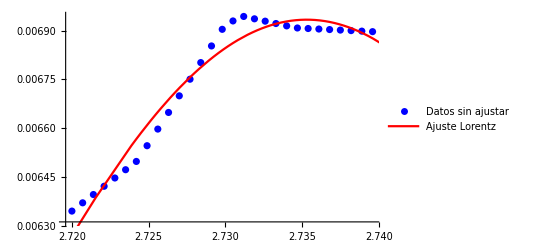

{A1→1.78×10^-3,ω01→2.74,γ1→9.4×10^-2}

{0.00178234,2.73571,0.0939665}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps30Data3=Table[{x,eps30Im[x]},{x,2.72,2.74,0.0007}];

fit301=NonlinearModelFit[eps30Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.01}},ω];

Show[ListPlot[eps30Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit301[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
        
ScientificForm[fit301["BestFitParameters"],3]
fit301Values=Values[fit301["BestFitParameters"]]
```

#### Ajuste total

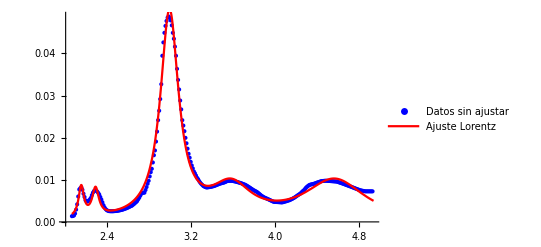

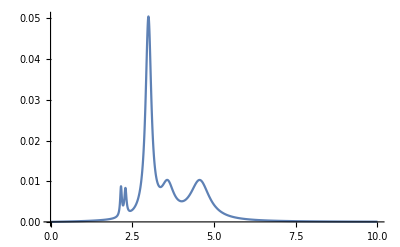

{A1→9.42×10^-4,ω01→2.16,γ1→6.09×10^-2,A2→1.15×10^-3,ω02→2.29,γ2→7.69×10^-2,A3→3.07×10^-2,ω03→3.,γ3→2.1×10^-1,A4→1.29×10^-2,ω04→3.59,γ4→4.69×10^-1,A5→3.15×10^-2,ω05→4.58,γ5→7.11×10^-1,A6→2.11×10^-7,ω06→2.7,γ6→5.37×10^-2}

```mathematica
fit30tot=NonlinearModelFit[eps30Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         A2>0 && 0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit30Values[[1]]},{ω01,fit30Values[[2]]},{γ1,fit30Values[[3]]},
                         {A2,fit30Values[[4]]},{ω02,fit30Values[[5]]},{γ2,fit30Values[[6]]},
                         {A3,fit30Values[[7]]},{ω03,fit30Values[[8]]},{γ3,fit30Values[[9]]},
                         {A4,fit30Values[[10]]},{ω04,fit30Values[[11]]},{γ4,fit30Values[[12]]},
                         {A5,fit30Values[[13]]},{ω05,fit30Values[[14]]},{γ5,fit30Values[[15]]},
                         {A6,fit301Values[[1]]},{ω06,fit301Values[[2]]},{γ6,fit301Values[[3]]}},
                         ω, Weights->(If[2.8<#<3.1,100,2]&/@(eps30Data[[All,1]]))];

Show[ListPlot[eps30Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
          Plot[fit30tot[ω],{ω,xmin30,xmax30},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

Plot[fit30tot[ω],{ω,0,10},PlotRange->All]

ScientificForm[fit30tot["BestFitParameters"],3]
```

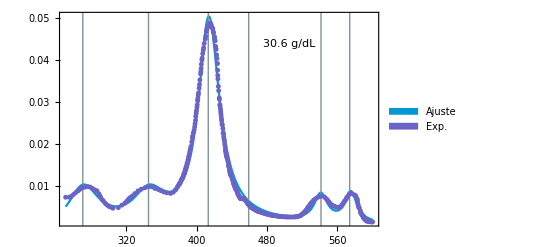

```mathematica
majorTicks30=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,{2.16,2.29,3,3.59,4.58,2.7}}];

interp30=Plot[fit30tot[h c/λ],{λ,h c/xmax30,h c/xmin30},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/2.16,0},{h c/2.16,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.29,0},{h c/2.29,1}}]},
                        {gris,InfiniteLine[{{h c/3,0},{h c/3,1}}]},
                        {gris,InfiniteLine[{{h c/3.59,0},{h c/3.59,1}}]},
                        {gris,InfiniteLine[{{h c/4.58,0},{h c/4.58,1}}]},
                        {gris,InfiniteLine[{{h c/2.7,0},{h c/2.7,1}}],
                        Inset[Style["30.6 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*)},
              Evaluate[Sequence @@ plotStyling]];
plotpoints30=ListPlot[{#[[1]],#[[2]]}&/@eps30DataLambda,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajuste30=Show[{interp30,plotpoints30}, FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks30}}]
```

```mathematica
Export["ajusteLorentz30.svg",ajuste30]
```

ajusteLorentz30.svg

### Parte real vía SSKK

```mathematica
parteIm030=Table[fit30[x],{x,1.19,4.96,0.01}];
parteIm03010=Table[fit30[x],{x,omega10}];
omegaprueba30=Range[2.11,4.95,0.01];

datosRealObjetivo30=eps30Re/@omegaprueba30;
                  funcionError30[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
                  epsAnchor=eps30Re[w];
                    (*ejecutar modelo*)espectro=sskkrebook[omegaprueba30,parteIm030,w,epsAnchor];
                      (*error cuadrático total*)dif=espectro-datosRealObjetivo30;
                    Sqrt[Total[dif^2]/Length[datosRealObjetivo30]]];
                    
error30=Table[{w,funcionError30[w]},{w,2.05,3.1,0.01}];
MinimalBy[error30,Last]
```

InterpolatingFunction::dmval: Input value {4.94} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,«275»}.

Set::setraw: Cannot assign to raw object 0.000293845.

Set::setraw: Cannot assign to raw object 0.000297845.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pspec1: Part specification NotFound is not applicable.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

Part::pspec1: Part specification NotFound is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

{{2.85,0.0398241}}

```mathematica
parteIm03010=Table[fit30[x],{x,omega10}];
```

```mathematica
parteReSSKK30=sskkrebook[omega10,parteIm03010,2.85,eps30Re[2.85]];
partere302=Interpolation[Transpose[{omega10,parteReSSKK30}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.88294×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

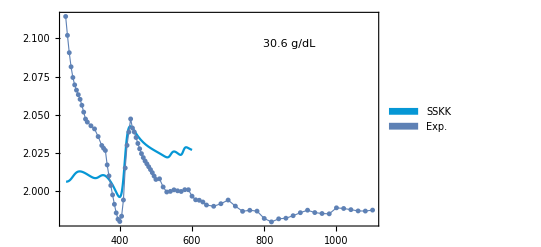

```mathematica
eps30DataRe=Table[{x,eps30Re[h c/x]},{x,datos1Beta[[All,1]]}];
majorTicks30 =Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}];

interp30sskk=Plot[partere302[h c/λ],{λ,h c/xmax30,h c/xmin30},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["30.6 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  Evaluate[Sequence @@ plotStyling]];

plotpoints30sskk=ListPlot[{#[[1]],#[[2]]}&/@eps30DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                          PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskk30=Show[{interp30sskk,plotpoints30sskk}, PlotRange->{{Automatic,600},{Automatic,2.12}}
                                  ,FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskk30.svg",sskk30]
```

sskk30.svg

```mathematica
epsEritrocitosData30=Table[{w*0.2418,partere302[w],fit30tot[w]},{w,1,10,0.01}];
Export["epsEritrocitosData30.csv",epsEritrocitosData30]
```

epsEritrocitosData30.csv

#### Cálculo de la desviación de SSKK de los datos experimentales

```mathematica
Mean[Table[partere302[w]-eps30Re[w],{w,2.07,3.1,0.01}]]
```

0.0144382

```mathematica
h c/800
```

1.5498

## Concentración 34 g/dL

### Importación de datos

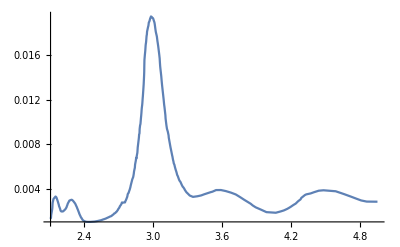

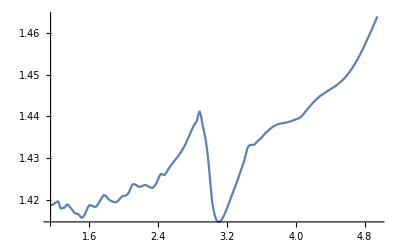

```mathematica
parteRe34[x_]:=parteRe[x,34];
parteIm34[x_]:=(34/30)*parteIm30[x];

Plot[parteIm34[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe34[x],{x,1.15,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

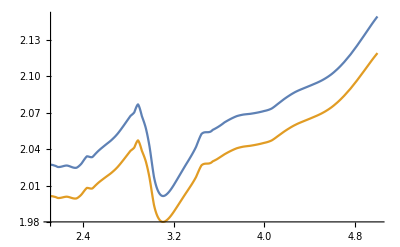

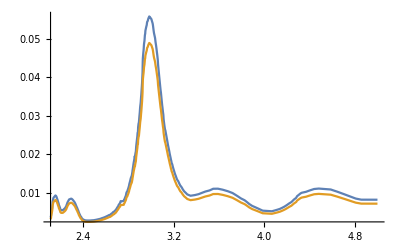

```mathematica
(*Función dieléctrica experimental*)
eps34Im[x_]:=Im[eps[parteRe34,parteIm34,x]];
eps34Re[x_]:=Re[eps[parteRe34,parteIm34,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos34={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};

ω0i34=ω0i[eps34Im,intervalos34,tolRes];

Plot[{eps34Re[x],eps30Re[x]},{x,2.11,5}]
Plot[{eps34Im[x],eps30Im[x]},{x,2.11,5},PlotRange->All]
```

```mathematica
ω0i34[[1]]
```

eps34Im

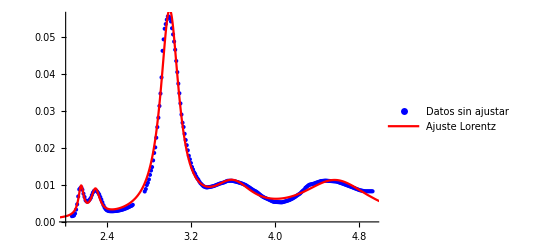

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};

eps34Data0=Table[{x,eps34Im[x]},{x,xmin30,2.65,0.01}];
eps34Data1=Table[{x,eps34Im[x]},{x,2.76,xmax30,0.01}];
eps34Data2=Join[eps34Data0,eps34Data1];

eps34Data=Table[{x,eps34Im[x]},{x,xmin30,xmax30,0.01}];
eps34DataLambda=Table[{x,eps34Im[h c/x]},{x,datos1uA30[[All,1]]}];

fit34 = NonlinearModelFit[eps34Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i34[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i34[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i34[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i34[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i34[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps34Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit34[ω],{ω,xmin30-0.5,xmax30+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit34[ω],{ω,0,10},PlotRange->All];

fit34Values=Values[fit34["BestFitParameters"]];
```

#### Ajuste pico pequeño

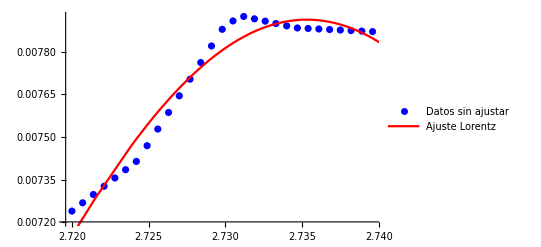

{A1→2.03×10^-3,ω01→2.74,γ1→9.4×10^-2}

{0.00203374,2.73572,0.0939647}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps34Data3=Table[{x,eps34Im[x]},{x,2.72,2.74,0.0007}];

fit341=NonlinearModelFit[eps34Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.01}},ω];

Show[ListPlot[eps34Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit341[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
        
ScientificForm[fit341["BestFitParameters"],3]
fit341Values=Values[fit341["BestFitParameters"]]
```

#### Ajuste total

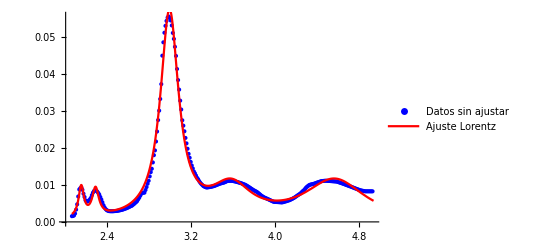

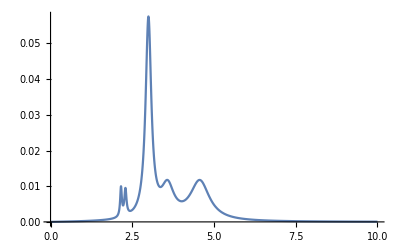

{A1→1.07×10^-3,ω01→2.16,γ1→6.09×10^-2,A2→1.31×10^-3,ω02→2.29,γ2→7.69×10^-2,A3→3.51×10^-2,ω03→3.,γ3→2.1×10^-1,A4→1.47×10^-2,ω04→3.59,γ4→4.7×10^-1,A5→3.59×10^-2,ω05→4.58,γ5→7.11×10^-1,A6→1.83×10^-7,ω06→2.7,γ6→5.42×10^-2}

```mathematica
fit34tot=NonlinearModelFit[eps34Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         A2>0 && 0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit34Values[[1]]},{ω01,fit34Values[[2]]},{γ1,fit34Values[[3]]},
                         {A2,fit34Values[[4]]},{ω02,fit34Values[[5]]},{γ2,fit34Values[[6]]},
                         {A3,fit34Values[[7]]},{ω03,fit34Values[[8]]},{γ3,fit34Values[[9]]},
                         {A4,fit34Values[[10]]},{ω04,fit34Values[[11]]},{γ4,fit34Values[[12]]},
                         {A5,fit34Values[[13]]},{ω05,fit34Values[[14]]},{γ5,fit34Values[[15]]},
                         {A6,fit341Values[[1]]},{ω06,fit341Values[[2]]},{γ6,fit341Values[[3]]}},
                         ω, Weights->(If[2.8<#<3.1,100,2]&/@(eps34Data[[All,1]]))];

Show[ListPlot[eps34Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
          Plot[fit34tot[ω],{ω,xmin30,xmax30},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

Plot[fit34tot[ω],{ω,0,10},PlotRange->All]

ScientificForm[fit34tot["BestFitParameters"],3]
```

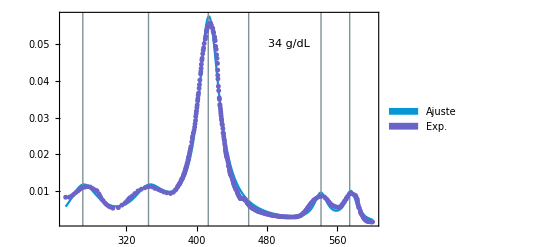

```mathematica
majorTicks34=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,{2.16,2.29,3,3.59,4.58,2.7}}];

interp34=Plot[fit34tot[h c/λ],{λ,h c/xmax30,h c/xmin30},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/2.16,0},{h c/2.16,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.29,0},{h c/2.29,1}}]},
                        {gris,InfiniteLine[{{h c/3,0},{h c/3,1}}]},
                        {gris,InfiniteLine[{{h c/3.59,0},{h c/3.59,1}}]},
                        {gris,InfiniteLine[{{h c/4.58,0},{h c/4.58,1}}]},
                        {gris,InfiniteLine[{{h c/2.7,0},{h c/2.7,1}}],
                        Inset[Style["34 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*)},
              Evaluate[Sequence @@ plotStyling]];
plotpoints34=ListPlot[{#[[1]],#[[2]]}&/@eps34DataLambda,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajuste34=Show[{interp34,plotpoints34}, FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks34}}]
```

```mathematica
Export["ajusteLorentz34.svg",ajuste34]
```

ajusteLorentz34.svg

### Parte real vía SSKK

```mathematica
parteIm034=Table[fit34tot[x],{x,1.19,4.96,0.01}];
parteIm03410=Table[fit34tot[x],{x,omega10}];
omegaprueba34=Range[2.11,4.95,0.01];

datosRealObjetivo34=eps34Re/@omegaprueba34;
                  funcionError34[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
                  epsAnchor=eps34Re[w];
                    (*ejecutar modelo*)espectro=sskkrebook[omegaprueba34,parteIm034,w,epsAnchor];
                      (*error cuadrático total*)dif=espectro-datosRealObjetivo34;
                    Sqrt[Total[dif^2]/Length[datosRealObjetivo34]]];
                    
error34=Table[{w,funcionError34[w]},{w,2.05,3.1,0.01}];
MinimalBy[error34,Last]
```

InterpolatingFunction::dmval: Input value {4.94} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,«275»}.

Set::setraw: Cannot assign to raw object 0.000310412.

Set::setraw: Cannot assign to raw object 0.000314665.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pspec1: Part specification NotFound is not applicable.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

Part::pspec1: Part specification NotFound is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

{{2.91,0.0423573}}

```mathematica
parteIm03410=Table[fit34tot[x],{x,omega10}];
```

```mathematica
parteReSSKK34=sskkrebook[omega10,parteIm03410,2.91,eps34Re[2.91]];
partere342=Interpolation[Transpose[{omega10,parteReSSKK34}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.97771×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

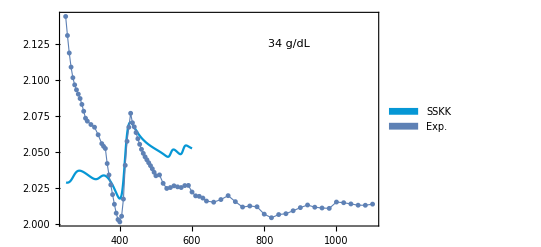

```mathematica
eps34DataRe=Table[{x,eps34Re[h c/x]},{x,datos1Beta[[All,1]]}];
majorTicks34 =Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}];

interp34sskk=Plot[partere342[h c/λ],{λ,h c/xmax30,h c/xmin30},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["34 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  Evaluate[Sequence @@ plotStyling]];

plotpoints34sskk=ListPlot[{#[[1]],#[[2]]}&/@eps34DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskk34=Show[{interp34sskk,plotpoints34sskk}, PlotRange->{{Automatic,600},{Automatic,2.16}},FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskk34.svg",sskk34]
```

sskk34.svg

```mathematica
epsEritrocitosData34=Table[{w*0.2418,partere342[w],fit34tot[w]},{w,1,10,0.01}];
Export["epsEritrocitosData34.csv",epsEritrocitosData34]
```

epsEritrocitosData34.csv

#### Cálculo de la desviación de SSKK de los datos experimentales

```mathematica
Mean[Table[partere342[w]-eps34Re[w],{w,2.07,3.1,0.01}]]
```

0.0138951

```mathematica
Mean[Table[partere342[w]-eps34Re[w],{w,2.07,4.93,0.01}]]
```

-0.0218218

## Concentración 32.9 g/dL

### Importación de datos

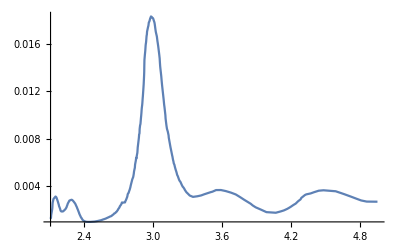

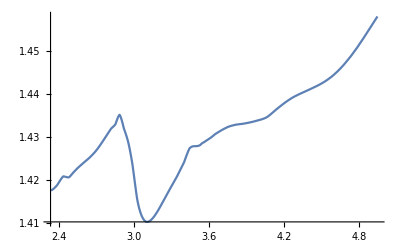

```mathematica
parteRe32[x_]:=parteRe[x,32];
parteIm32[x_]:=(32/30)*parteIm30[x];

Plot[parteIm32[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe32[x],{x,2.33,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

#### Ajuste sin el pico pequeño

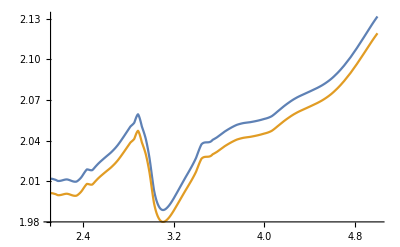

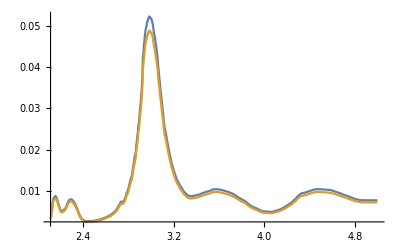

```mathematica
(*Función dieléctrica experimental*)
eps32Im[x_]:=Im[eps[parteRe32,parteIm32,x]];
eps32Re[x_]:=Re[eps[parteRe32,parteIm32,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos32={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};

ω0i32=ω0i[eps32Im,intervalos32,tolRes];

Plot[{eps32Re[x],eps30Re[x]},{x,2.11,5}]
Plot[{eps32Im[x],eps30Im[x]},{x,2.11,5},PlotRange->All]
```

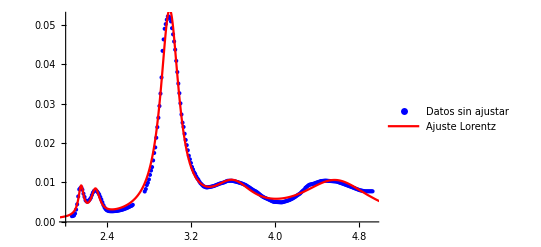

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
{xmin32,xmax32}={Min[datos2im30],Max[datos2im30]};

eps32Data0=Table[{x,eps32Im[x]},{x,xmin32,2.65,0.01}];
eps32Data1=Table[{x,eps32Im[x]},{x,2.76,xmax32,0.01}];
eps32Data2=Join[eps32Data0,eps32Data1];

eps32Data=Table[{x,eps32Im[x]},{x,xmin32,xmax32,0.01}];
eps32DataLambda=Table[{x,eps32Im[h c/x]},{x,datos1uA30[[All,1]]}];

fit32 = NonlinearModelFit[eps32Data2,
                           lorentzSumIm[ω, {A1, A2, A3, A4, A5}, {ω01, ω02, ω03, ω04, ω05}, {γ1, γ2, γ3, γ4, γ5} ], 
             
                          {{A1, 0.01}, {ω01, ω0i32[[1]]}, {γ1, 0.05}, 
                           {A2, 0.01}, {ω02, ω0i32[[2]]}, {γ2, 0.1}, 
                           {A3, 0.01}, {ω03, ω0i32[[3]]}, {γ3, 0.1}, 
                           {A4, 0.01}, {ω04, ω0i32[[4]]}, {γ4, 0.1}, 
                            {A5, 0.01}, {ω05, ω0i32[[5]]}, {γ5, 0.1}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps32Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fit32[ω],{ω,xmin32-0.5,xmax32+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
              
Plot[fit32[ω],{ω,0,10},PlotRange->All];

fit32Values=Values[fit32["BestFitParameters"]];
```

#### Ajuste pico pequeño

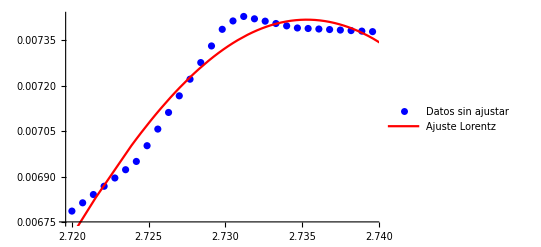

{A1→1.91×10^-3,ω01→2.74,γ1→9.4×10^-2}

{0.0019065,2.73571,0.0939657}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps32Data3=Table[{x,eps32Im[x]},{x,2.72,2.74,0.0007}];

fit321=NonlinearModelFit[eps32Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.01}},ω];

Show[ListPlot[eps32Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
        Plot[fit321[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
        
ScientificForm[fit321["BestFitParameters"],3]
fit321Values=Values[fit321["BestFitParameters"]]
```

#### Ajuste total

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

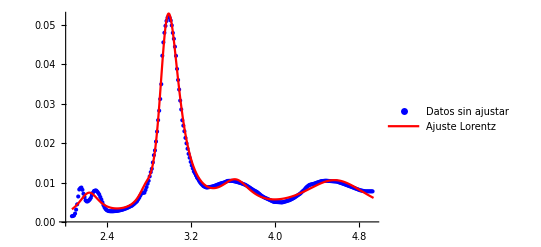

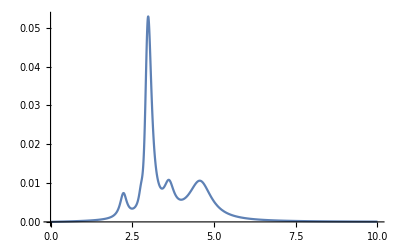

{A1→-1.6,ω01→2.95,γ1→3.09×10^-1,A2→3.46×10^-3,ω02→2.23,γ2→2.5×10^-1,A3→1.63,ω03→2.95,γ3→3.07×10^-1,A4→1.01×10^-2,ω04→3.63,γ4→3.79×10^-1,A5→3.89×10^-2,ω05→4.59,γ5→8.44×10^-1,A6→1.99×10^-3,ω06→2.77,γ6→1.71×10^-1}

```mathematica
fit32tot=NonlinearModelFit[eps32Data,{lorentzSumIm[ω, {A1, A2, A3, A4, A5,A6}, {ω01, ω02, ω03, ω04, ω05,ω06}, {γ1, γ2, γ3, γ4, γ5,γ6} ], 
                         A2>0 && 0.002>A6>0 && 0.2>γ6>0 && 2.77>ω06>2.66}, 
                         {{A1,fit32Values[[1]]},{ω01,fit32Values[[2]]},{γ1,fit32Values[[3]]},
                         {A2,fit32Values[[4]]},{ω02,fit32Values[[5]]},{γ2,fit32Values[[6]]},
                         {A3,fit32Values[[7]]},{ω03,fit32Values[[8]]},{γ3,fit32Values[[9]]},
                         {A4,fit32Values[[10]]},{ω04,fit32Values[[11]]},{γ4,fit32Values[[12]]},
                         {A5,fit32Values[[13]]},{ω05,fit32Values[[14]]},{γ5,fit32Values[[15]]},
                         {A6,fit321Values[[1]]},{ω06,fit321Values[[2]]},{γ6,fit321Values[[3]]}},
                         ω, Weights->(If[2.8<#<3.1,100,2]&/@(eps32Data[[All,1]]))];

Show[ListPlot[eps32Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
          Plot[fit32tot[ω],{ω,xmin30,xmax30},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

Plot[fit32tot[ω],{ω,0,10},PlotRange->All]

ScientificForm[fit32tot["BestFitParameters"],3]
```

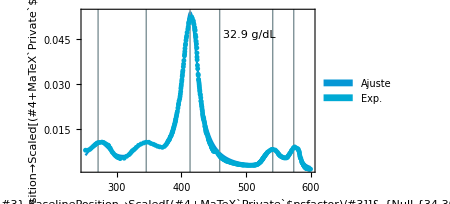

```mathematica
majorTicks32=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,{2.16,2.29,3,3.59,4.58,2.7}}];

interp32=Plot[fit32[h c/λ],{λ,h c/xmax30,h c/xmin30},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/2.16,0},{h c/2.16,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.29,0},{h c/2.29,1}}]},
                        {gris,InfiniteLine[{{h c/3,0},{h c/3,1}}]},
                        {gris,InfiniteLine[{{h c/3.59,0},{h c/3.59,1}}]},
                        {gris,InfiniteLine[{{h c/4.58,0},{h c/4.58,1}}]},
                        {gris,InfiniteLine[{{h c/2.7,0},{h c/2.7,1}}],
                        Inset[Style["32.9 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*)},
              Evaluate[Sequence @@ plotStyling]];
plotpoints32=ListPlot[{#[[1]],#[[2]]}&/@eps32DataLambda,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajuste32=Show[{interp32,plotpoints32}, FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicks32}}]
```

```mathematica
Export["ajusteLorentz34.svg",ajuste34]
```

ajusteLorentz34.svg

### Parte real vía SSKK

```mathematica
parteIm032=Table[fit32[x],{x,1.19,4.96,0.01}];
parteIm03210=Table[fit32[x],{x,omega10}];
omegaprueba32=Range[2.11,4.95,0.01];

datosRealObjetivo32=eps32Re/@omegaprueba32;
                  funcionError32[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
                  epsAnchor=eps32Re[w];
                    (*ejecutar modelo*)espectro=sskkrebook[omegaprueba32,parteIm032,w,epsAnchor];
                      (*error cuadrático total*)dif=espectro-datosRealObjetivo32;
                    Sqrt[Total[dif^2]/Length[datosRealObjetivo32]]];
                    
error32=Table[{w,funcionError32[w]},{w,2.05,3.1,0.01}];
MinimalBy[error32,Last]
```

InterpolatingFunction::dmval: Input value {4.94} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,«275»}.

Set::setraw: Cannot assign to raw object 0.000314265.

Set::setraw: Cannot assign to raw object 0.000318544.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pspec1: Part specification NotFound is not applicable.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

Part::pspec1: Part specification NotFound is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

{{2.85,0.0409708}}

```mathematica
parteIm03210=Table[fit32[x],{x,omega10}];
```

```mathematica
parteReSSKK32=sskkrebook[omega10,parteIm03210,2.91,eps32Re[2.91]];
partere322=Interpolation[Transpose[{omega10,parteReSSKK32}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 2.01382×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

LinkOpen::linke: Could not find MathLink executable.

MapThread::mptd: Object Null at position {2, 1} in MapThread[Show[#1,ImageSize→{#2,#3},BaselinePosition→Scaled[(Slot[«1»]+MaTeX`Private`$psfactor)/Slot[«1»]]]&,{Null,{49.1759},{16.3387},{4.3039}}] has only 0 of required 1 dimensions.

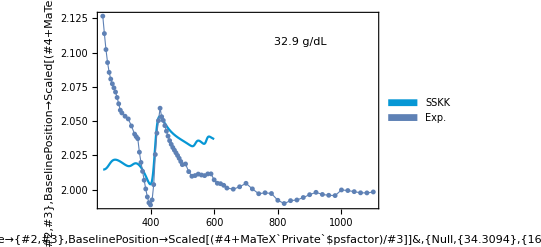

```mathematica
eps32DataRe=Table[{x,eps32Re[h c/x]},{x,datos1Beta[[All,1]]}];
majorTicks32 =Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[250,600,50]}];

interp32sskk=Plot[partere322[h c/λ],{λ,h c/xmax30,h c/xmin30},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["32.9 g/dL",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  Evaluate[Sequence @@ plotStyling]];

plotpoints32sskk=ListPlot[{#[[1]],#[[2]]}&/@eps32DataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskk32=Show[{interp32sskk,plotpoints32sskk}, PlotRange->{{Automatic,600},{Automatic,2.16}},FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskk34.svg",sskk34]
```

sskk34.svg

```mathematica
epsEritrocitosData32=Table[{w*0.2418,partere322[w],fit32[w]},{w,1,10,0.01}];
Export["epsEritrocitosData32.csv",epsEritrocitosData32]
```

epsEritrocitosData32.csv

```mathematica
epsEritrocitosData32lambda=Table[{h c/w,partere322[w],fit32[w]},{w,1,10,0.01}];
Export["epsEritrocitosData32lambda.csv",epsEritrocitosData32lambda]
```

epsEritrocitosData32lambda.csv

#### Cálculo de la desviación de SSKK de los datos experimentales

```mathematica
Mean[Table[partere342[w]-eps34Re[w],{w,2.07,3.1,0.01}]]
```

0.0138951

```mathematica
Mean[Table[partere342[w]-eps34Re[w],{w,2.07,4.93,0.01}]]
```

-0.0218218

## Plasma

### Importación de datos

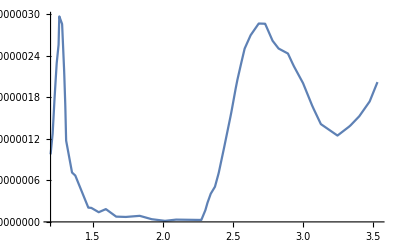

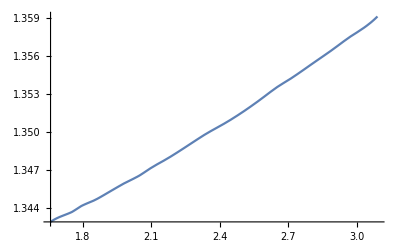

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuAPlasma=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\uA_ImN_Plasma.csv"];
datosRePlasma=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\ReN_Plasma.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uAPlasma=Drop[datosuAPlasma,1];
datos1RePlasma=Drop[datosRePlasma,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2imPlasma=h c/datos1uAPlasma[[All,1]];
datos2rePlasma=h c/datos1RePlasma[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3imPlasma=datos1uAPlasma[[All,2]]*10^(-6)*datos1uAPlasma[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteImPlasma=Interpolation[Transpose[{datos2imPlasma,datos3imPlasma}],InterpolationOrder->1];
parteRePlasma=Interpolation[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]];

Plot[parteImPlasma[x],{x,1.2,3.53}]
Plot[parteRePlasma[x],{x,1.66,3.09},PlotRange->All]
```

### Ajuste de lorentzianas

InterpolatingFunction::dmval: Input value {1.2382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.2618} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.60003} lies outside the range of data in the interpolating function. Extrapolation will be used.

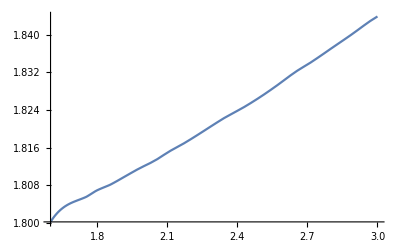

InterpolatingFunction::dmval: Input value {1.60003} lies outside the range of data in the interpolating function. Extrapolation will be used.

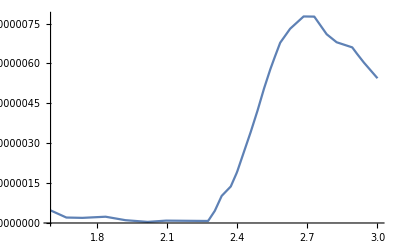

```mathematica
(*Función dieléctrica experimental*)
epsPlasmaIm[x_]:=Im[eps[parteRePlasma,parteImPlasma,x]];
epsPlasmaRe[x_]:=Re[eps[parteRePlasma,parteImPlasma,x]];

(*Intervalos de búsqueda de los máximos*)
intervalosPlasma={{1.2,1.3},{2.57,2.8},{2.8,2.9},{3.4,3.5}};

ω0iPlasma=ω0i[epsPlasmaIm,intervalosPlasma,tolRes];

Plot[epsPlasmaRe[x],{x,1.6,3}]
Plot[epsPlasmaIm[x],{x,1.6,3},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {1.13393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.13493} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.13593} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.52268} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.47441} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.40027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

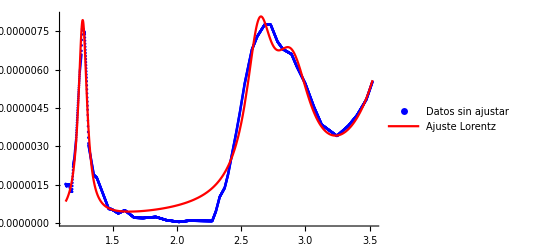

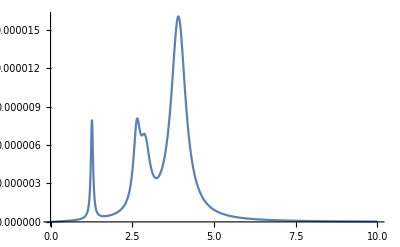

{7.96108×10^-7,1.26727,0.0813009,3.74032×10^-6,2.64261,0.247444,4.98805×10^-6,2.8966,0.36797,0.0000333575,3.92042,0.537582}

{A1→7.96×10^-7,ω01→1.27,γ1→8.13×10^-2,A2→3.74×10^-6,ω02→2.64,γ2→2.47×10^-1,A3→4.99×10^-6,ω03→2.9,γ3→3.68×10^-1,A4→3.34×10^-5,ω04→3.92,γ4→5.38×10^-1}

```mathematica
{xminPlasma,xmaxPlasma}={Min[datos2imPlasma],Max[datos2imPlasma]};

epsPlasmaData=Table[{x,epsPlasmaIm[x]},{x,xminPlasma,xmaxPlasma,0.001}];
epsPlasmaDataLambda=Table[{x,epsPlasmaIm[h c/x]},{x,datos1uAPlasma[[All,1]]}];

fitPlasma = NonlinearModelFit[epsPlasmaData,
                           {lorentzSumIm[ω, {A1, A2, A3, A4}, {ω01, ω02, ω03, ω04}, {γ1, γ2, γ3, γ4} ]}, 
             
                          {{A1,0.001},{ω01,ω0iPlasma[[1]]},{γ1,0.05},
                          {A2,0.000001},{ω02,ω0iPlasma[[2]]},{γ2,0.05},
                          {A3,0.000001},{ω03,ω0iPlasma[[3]]},{γ3,0.05},
                          {A4,0.001},{ω04,4.1},{γ4,0.07}}, 
                            ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[epsPlasmaData,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitPlasma[ω],{ω,xminPlasma,xmaxPlasma},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All],PlotRange->All]
              
Plot[fitPlasma[ω],{ω,0,10},PlotRange->All]

fitPlasmaValues=Values[fitPlasma["BestFitParameters"]]
ScientificForm[fitPlasma["BestFitParameters"],3]
```

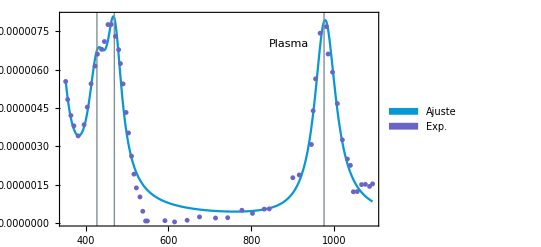

```mathematica
majorTicksPlasma=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,{1.27,2.64,2.9,3.92}}];

interpPlasma=Plot[fitPlasma[h c/λ],{λ,h c/xmaxPlasma,h c/xminPlasma},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Epilog->{{gris,InfiniteLine[{{h c/1.27,0},{h c/1.27,1}}]},(*línea en x1*)
                        {gris,InfiniteLine[{{h c/2.64,0},{h c/2.64,1}}]},
                        {gris,InfiniteLine[{{h c/2.9,0},{h c/2.9,1}}]},
                        {gris,InfiniteLine[{{h c/3.92,0},{h c/3.92,1}}]},
                        Inset[Style["Plasma",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]]}(*línea en y=-0.5*),
                        ImagePadding->{{100,15},{60,60}},
              Evaluate[Sequence @@ plotStyling]];
plotpointsPlasma=ListPlot[{#[[1]],#[[2]]}&/@epsPlasmaDataLambda,PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                    LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                                    Evaluate[Sequence @@ plotStyling]];

ajustePlasma=Show[{interpPlasma,plotpointsPlasma}, FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,majorTicksPlasma}}]
```

```mathematica
Export["ajustePlasma.svg",ajustePlasma]
```

ajustePlasma.svg

### Parte real vía SSKK

```mathematica
parteIm0Plasma=Table[fitPlasma[x],{x,2.11,4.95,0.01}];
parteIm0Plasma10=Table[fitPlasma[x],{x,omega10}];
omegapruebaPlasma=Range[2.11,4.95,0.01];

datosRealObjetivoPlasma=epsPlasmaRe/@omegapruebaPlasma;
                  funcionErrorPlasma[w_?NumericQ]:=Module[{epsAnchor,espectro,dif},(*valor de epsReal en el ancla*)
                  epsAnchor=epsPlasmaRe[w];
                    (*ejecutar modelo*)espectro=sskkrebook[omegapruebaPlasma,parteIm0Plasma,w,epsAnchor];
                      (*error cuadrático total*)dif=espectro-datosRealObjetivoPlasma;
                    Sqrt[Total[dif^2]/Length[datosRealObjetivoPlasma]]];
                    
errorPlasma=Table[{w,funcionErrorPlasma[w]},{w,2.05,3.09,0.01}];
MinimalBy[errorPlasma,Last]
```

InterpolatingFunction::dmval: Input value {3.09} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.11} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,«275»}.

Set::setraw: Cannot assign to raw object 8.63558×10^-7.

Set::setraw: Cannot assign to raw object 8.84067×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Part::pspec1: Part specification NotFound is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.09} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{3.09,1.88642}}

```mathematica
parteIm0Plasma10=Table[fitPlasma[x],{x,omega10}];
```

```mathematica
parteReSSKKPlasma=sskkrebook[omega10,parteIm0Plasma10,2.88,epsPlasmaRe[2.88]];
parterePlasma2=Interpolation[Transpose[{omega10,parteReSSKKPlasma}]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«991»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.46062×10^-9.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

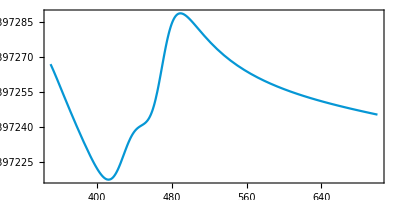

```mathematica
plotinsetPlasma=Plot[parterePlasma2[h c/λ],{λ,350,700},
                  PlotStyle->blueUNAM,FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},AspectRatio->1/2,
                  Evaluate[Sequence @@ plotStyling]]
```

InterpolatingFunction::dmval: Input value {1.13393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.18393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.23393} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

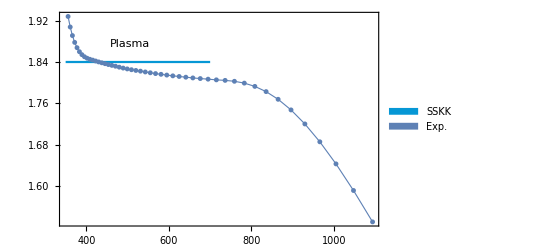

```mathematica
epsPlasmaDataRe=Table[{x,epsPlasmaRe[x]},{x,xminPlasma,xmaxPlasma,0.05}];
majorTicksPlasma =Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[350,700,50]}];

interpPlasmasskk=Plot[parterePlasma2[h c/λ],{λ,350,700},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.215,0.63}],
                  Epilog->{Inset[Style["Plasma",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.22, 0.85}]],
                           Inset[plotinsetPlasma,Scaled[{0.65, 0.7}]]},
                  Evaluate[Sequence @@ plotStyling]];

plotpointsPlasmasskk=ListPlot[{h c/#[[1]],#[[2]]}&/@epsPlasmaDataRe,
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.2,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskkPlasma=Show[{interpPlasmasskk,plotpointsPlasmasskk}, PlotRange->{{Automatic,700},{1.81,1.94}},FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskkPlasma0.svg",sskkPlasma]
```

sskkPlasma0.svg

#### Cálculo de la desviación de SSKK de los datos experimentales

```mathematica
Mean[Table[parterePlasma2[w]-epsPlasmaRe[w],{w,2.07,3.01,0.01}]]
```

0.011101

### Función dieléctrica final

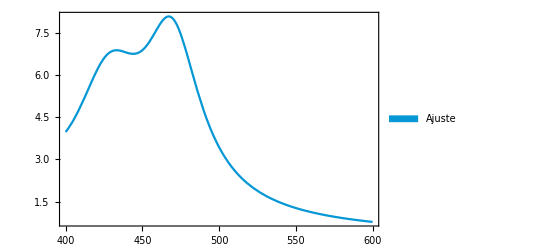

```mathematica
imPlasma=Plot[fitPlasma[h c/λ]*10^(6),{λ,400,600},PlotStyle->blueUNAM,
              PlotLegends->Placed[SwatchLegend[{Style["Ajuste",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
                        ImagePadding->{{100,15},{60,60}},
               FrameLabel->{{Style[MaTeX["\\text{Im}\\{\\varepsilon(\\lambda)\\}[\\times 10^{-6}]"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                Evaluate[Sequence @@ plotStyling]]
```

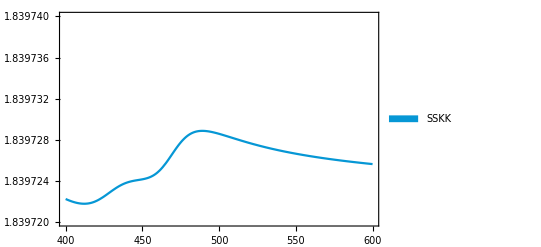

```mathematica
rePlasma=Plot[parterePlasma2[h c/λ],{λ,400,600},
                  PlotStyle->blueUNAM,
                  PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.215,0.63}],
                 FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                  PlotRange->{{400,600},{1.83972,1.83974}},
                  ImagePadding->{{90,15},{60,60}},
                  Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["RePlasma.svg",rePlasma]
Export["ImPlasma.svg",imPlasma]
```

RePlasma.svg

ImPlasma.svg

## Todas las concentraciones

```mathematica
h2olambda=Interpolation[Transpose[{datos1H2O[[All,1]]*1000,datos1H2O[[All,2]]}]];
betalambda=Interpolation[Transpose[{datos1Beta[[All,1]],datos1Beta[[All,2]]}]];
(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRelambda[x_,C_]:=h2olambda[x]*((betalambda[x]*C)+1);
parteRe28lambda[x_]:=parteRelambda[x,28.7];
parteRe34lambda[x_]:=parteRelambda[x,34];
parteRe30lambda[x_]:=parteRelambda[x,30.6];
parteRe32lambda[x_]:=parteRelambda[x,32.9];
```

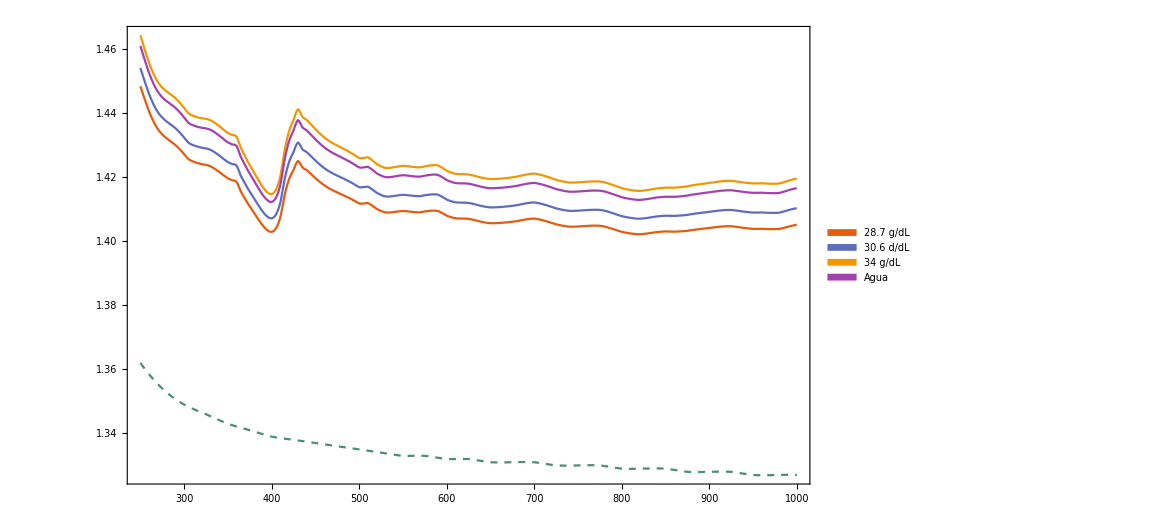

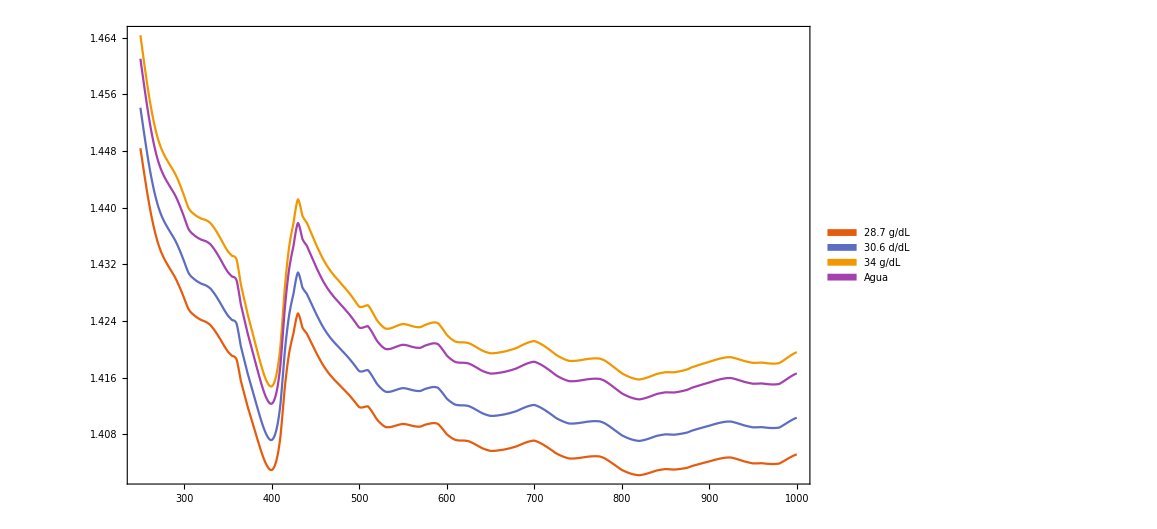

```mathematica
refTicks=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[200,1000,100]}];


refractiveIndex=Plot[{parteRe28lambda[λ],parteRe30lambda[λ],parteRe34lambda[λ],parteRe32lambda[λ],Style[h2olambda[λ],Dashed]},{λ,250,1000},
                  PlotLegends->Placed[SwatchLegend[{Style["28.7 g/dL",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["30.6 d/dL",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["34 g/dL",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["Agua",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.715,0.63}],
                  ImagePadding->{{90,13},{60,60}},
                  FrameLabel->{{Style[MaTeX["\\eta(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                  Evaluate[Sequence @@ plotStyling]]
                  
refractiveIndex=Plot[{parteRe28lambda[λ],parteRe30lambda[λ],parteRe34lambda[λ],parteRe32lambda[λ]},{λ,250,1000},
                  PlotLegends->Placed[SwatchLegend[{Style["28.7 g/dL",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["30.6 d/dL",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["34 g/dL",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["Agua",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,
                                                Spacings->0.05,
                                                LegendLayout->{"Column",1}],{0.715,0.63}],
                  ImagePadding->{{90,13},{60,60}},
                  FrameLabel->{{Style[MaTeX["\\eta(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                  Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["refractiveIndex.svg",refractiveIndex]
```

refractiveIndex.svg

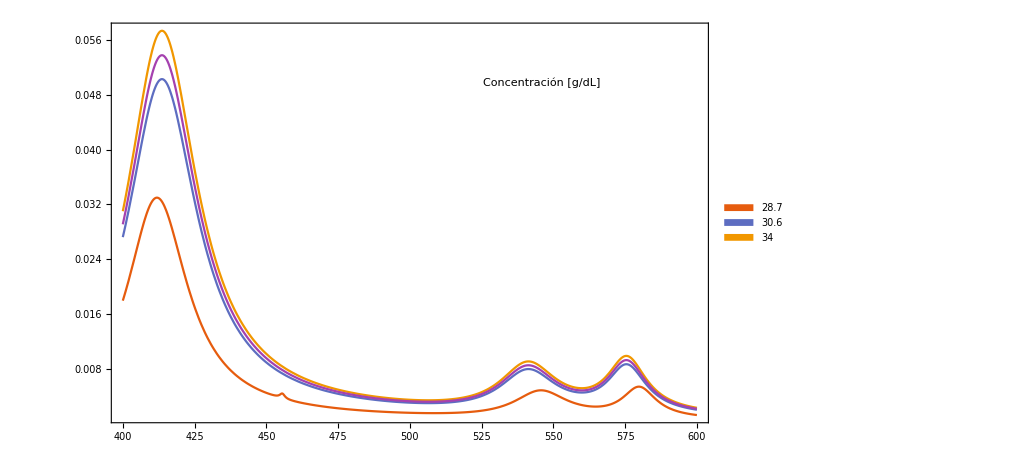

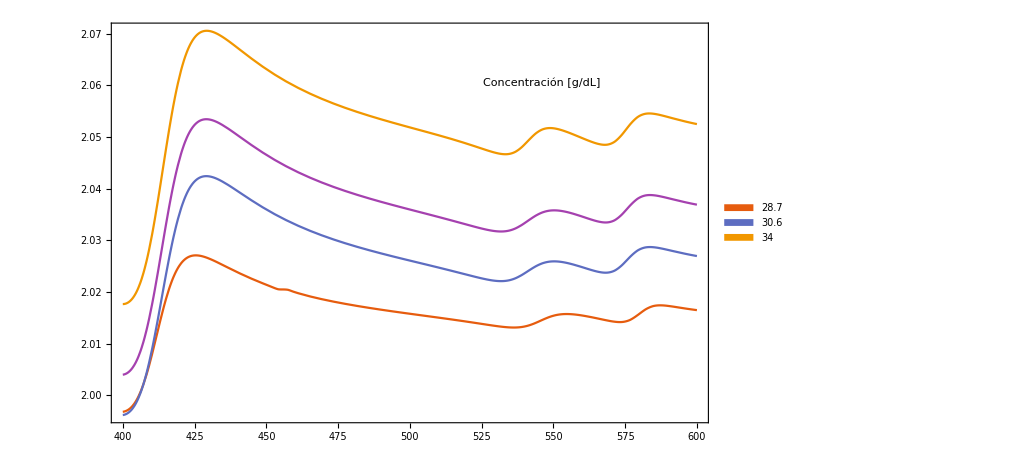

```mathematica
imTicks=Table[{h c/ev,NumberForm[ev,{Infinity,2}]},{ev,h c/Range[400,600,50]}];

parteImEri=Plot[{fit28tot[h c/λ],fit30[h c/λ],fit34[h c/λ],fit32[h c/λ]},{λ,400,600},
                  PlotLegends->Placed[SwatchLegend[{Style["28.7",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["30.6",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["34",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["Concentración [g/dL]",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  FrameLabel->{{Style[MaTeX["\\varepsilon''(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                  Evaluate[Sequence @@ plotStyling]]
                  
                  
parteReEri=Plot[{partere282[h c/λ],partere302[h c/λ],partere342[h c/λ],partere322[h c/λ]},{λ,400,600},
                  PlotLegends->Placed[SwatchLegend[{Style["28.7",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["30.6",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                                Style["34",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.715,0.63}],
                  Epilog->Inset[Style["Concentración [g/dL]",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.72, 0.85}]],
                  FrameLabel->{{Style[MaTeX["\\varepsilon'(\\lambda) "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                  Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["parteImEri.svg",parteImEri]
Export["parteReEri.svg",parteReEri]
```

parteImEri.svg

parteReEri.svg

## Datos del review con SSKK

```mathematica
datosReview0=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\review_N_reported_KK.csv"];
datosReview1=Drop[datosReview0,1];
datosReview=Interpolation[Transpose[{datosReview1[[All,1]],datosReview1[[All,2]]}],InterpolationOrder->1]
datosFriebel0=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\review_N_reported_Friebel.csv"];
datosFriebel1=Drop[datosFriebel0,1];
datosFriebel=Interpolation[Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}],InterpolationOrder->1];
```

InterpolatingFunction[…]

```mathematica
listReview=Table[{l,datosReview[l]},{l,400,600}];
listFriebel=Table[{l,datosFriebel[l]},{l,400,600}];
```

```mathematica
Mean[Abs[listReview[[All,2]]-listFriebel[[All,2]]]]
```

0.0210577

```mathematica
h c/800
```

1.5498

```mathematica
eps28tot[x_]:=partere282[x] + I fit28tot[x]
ir28tot[x_]:=Sqrt[eps28tot[h c/x]]
```

```mathematica
listsskk28=Table[{l,ir28tot[l]},{l,400,700}];
```

InterpolatingFunction::dmval: Input value {350.018} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

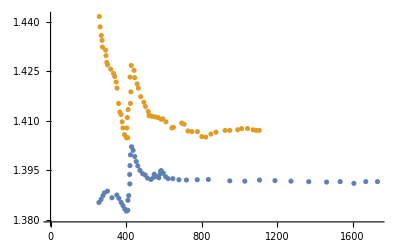

```mathematica
Show[ListPlot[{Transpose[{datosReview1[[All,1]],datosReview1[[All,2]]}],Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}]}],Plot[{Re[ir28tot[h c/x]]},{x,350,1250},PlotRange->All]]
```

```mathematica
h c/2.27
```

546.186

```mathematica
datosReview[350]
Re[ir28tot[h c/350]]
```

1.38752

InterpolatingFunction::dmval: Input value {350.} lies outside the range of data in the interpolating function. Extrapolation will be used.

5.36539×10^-14

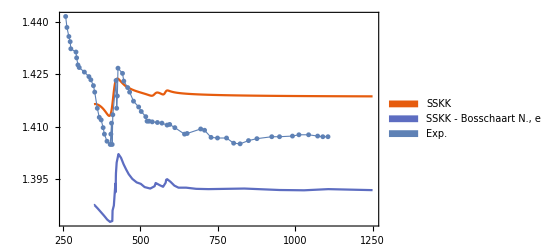

```mathematica
plotsskkYo=Plot[{Re[ir28tot[x]],datosReview[x]},{x,350,1250},
                   PlotLegends->Placed[SwatchLegend[{Style["SSKK",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                               Style["SSKK - Bosschaart N., et al. 2013",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.53,0.87}],
                
                  Evaluate[Sequence @@ plotStyling]];

listplotsskkYo=ListPlot[Transpose[{datosFriebel1[[All,1]],datosFriebel1[[All,2]]}],
                          PlotMarkers->{"●",5},
                          PlotLegends->Placed[SwatchLegend[{Style["Exp.",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                          LegendMarkerSize->{15,5},LegendMargins->0,Spacings->0.05],{0.7,0.73}],
                           PlotStyle->Thickness[0.002],                                
                          Joined->True,
                          Evaluate[Sequence @@ plotStyling]];

sskkComp=Show[{plotsskkYo,listplotsskkYo}, PlotRange->{{350,600},{Automatic,1.43}},FrameLabel->{{Style[MaTeX["\\text{Re}\\{\\varepsilon(\\lambda)\\}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export["sskkComp.svg",sskkComp]
```

sskkComp.svg